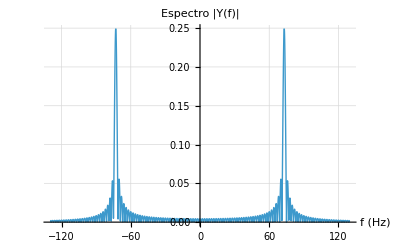

```mathematica
sinc[x_]:=Sin[x]/x

T=0.5;
f0=73;

Plot[Abs[(T/2)*(sinc[Pi*T*(f-f0)]+sinc[Pi*T*(f+f0)])],{f,-130,130},PlotRange->All,AxesLabel->{"f (Hz)"},PlotLabel->"Espectro |Y(f)|",PlotStyle->Thick,GridLines->Automatic]
```